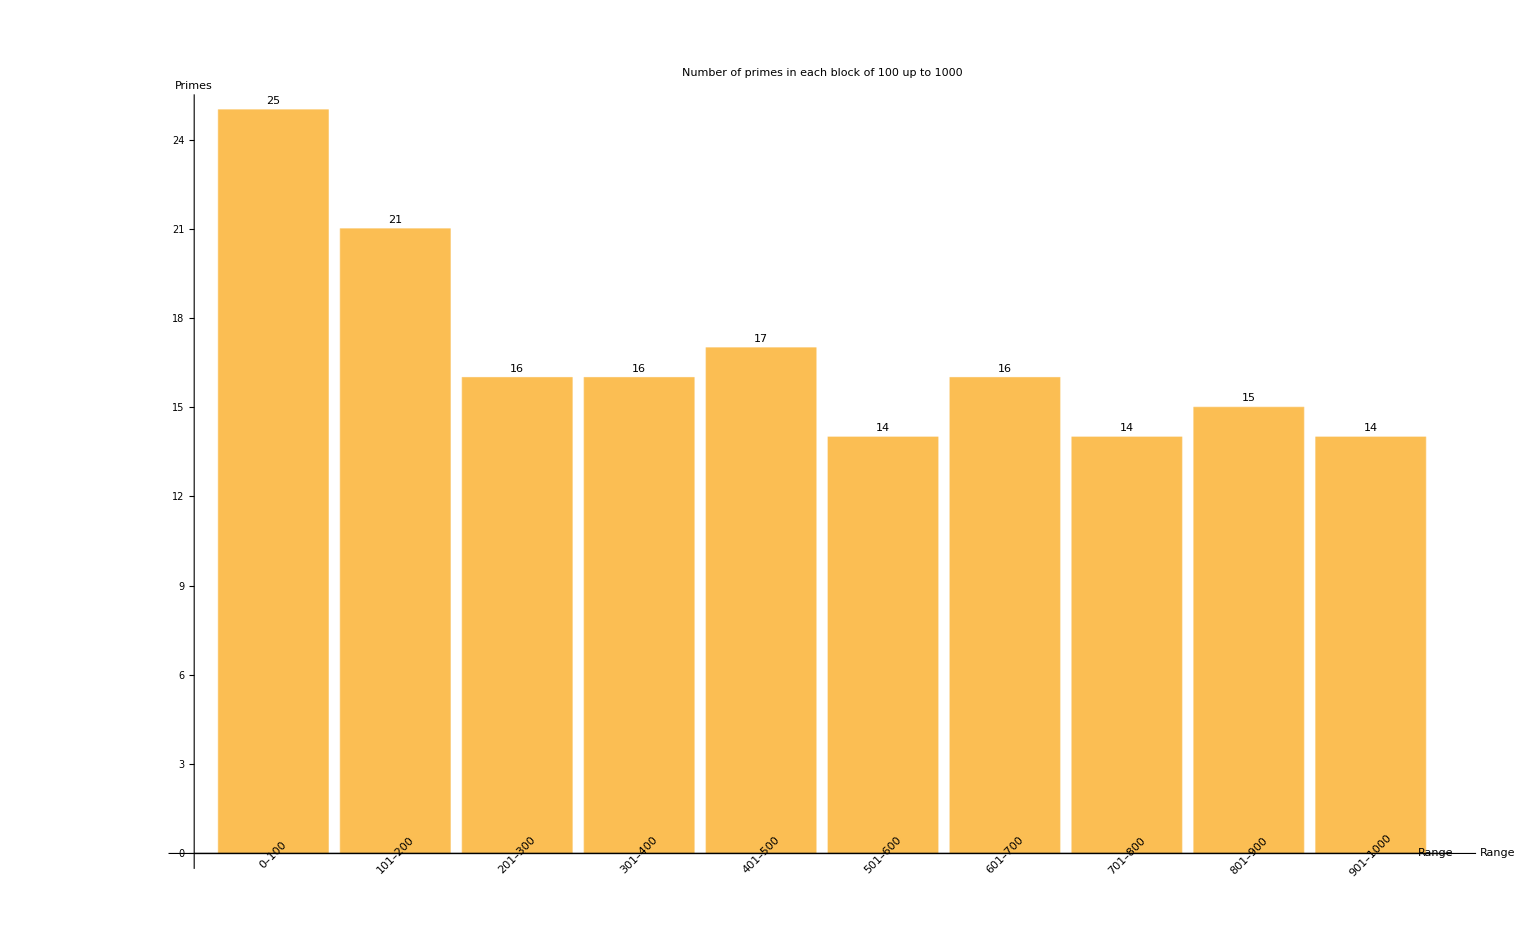

```mathematica
counts=Table[PrimePi[100 k]-PrimePi[100 (k-1)],{k,1,10}];
labels=Table[ToString[If[k==1,0,100 (k-1)+1]]<>"–"<>ToString[100 k],{k,1,10}];

BarChart[counts,ChartLabels->Placed[labels,Axis,Rotate[#,Pi/4]&],LabelingFunction->Above,AxesLabel->{"Range","Primes"},PlotLabel->"Number of primes in each block of 100 up to 1000",ImageSize->Large]
```